## Magnetic field

```mathematica
(* Modified 𝔹 in the interior of the magnet which should be multiplied by preFactor=2/3*μ0*M01 ... *)
(* In spherical eigen-coordinates AND spherical eigen-components *)
𝔹InnerSph[r_,ϑ_,φ_]:={Cos[ϑ],-Sin[ϑ],0};
𝔹OuterSph[r_,ϑ_,φ_]:=1/r^3*{Cos[ϑ],1/2*Sin[ϑ],0};
(* in eigen-cartesian basis and eigen-cartesian coordinates *)

(* Spherical basis vectors in the eigen system (both, coordinates and directions) *)
𝕖r[ϑ_,φ_]:={Sin[ϑ]*Cos[φ],Sin[ϑ]*Sin[φ],Cos[ϑ]};
𝕖ϑ[ϑ_,φ_]:={Cos[ϑ]*Cos[φ],Cos[ϑ]*Sin[φ],-Sin[ϑ]};
𝕖φ[ϑ_,φ_]:={-Sin[φ],Cos[φ],0};

𝔹InnerCart[x_,y_,z_]:=(
{0,0,1}
);
𝔹OuterCart[x_,y_,z_]:=(
rVal=Sqrt[x^2+y^2+z^2];
ϑVal=ArcTan[z,Sqrt[x^2+y^2]];
φVal=ArcTan[x,y];
{Br,Bϑ,Bφ}=𝔹OuterSph[rVal,ϑVal,φVal];
Br*𝕖r[ϑVal,φVal]+Bϑ*𝕖ϑ[ϑVal,φVal]+Bφ*𝕖φ[ϑVal,φVal]
);
```

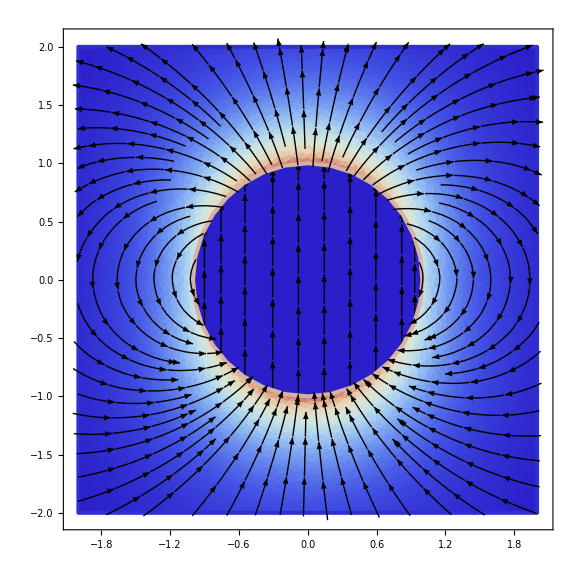

```mathematica
ballMagnet=Disk[];
ballMagnetBoundary=Circle[];
canvas=Rectangle[{-2,-2},{2,2}];
BplotOuter[y0_,z0_]=𝔹OuterCart[0,y0,z0][[{2,3}]];
outerPlot=StreamDensityPlot[Evaluate@BplotOuter[y0,z0],{y0,z0}∈RegionDifference[canvas,ballMagnet],ColorFunction->ColorData["ThermometerColors"], StreamStyle->Black,StreamColorFunction->None,AspectRatio->Automatic,BoundaryStyle->{Black,Thickness[0.005]}];
BplotInner[y0_,z0_]=𝔹InnerCart[0,y0,z0][[{2,3}]];
innerPlot=StreamDensityPlot[Evaluate@BplotInner[y0,z0],{y0,z0}∈ballMagnet,ColorFunction->ColorData["ThermometerColors"],StreamStyle->Black,StreamColorFunction->None,StreamPoints->10,StreamScale->0.12,AspectRatio->Automatic,BoundaryStyle->{Black,Thickness[0.005]}];
ballMagnetPlot=Show[innerPlot,outerPlot,PlotRange->All,ImageSize->Large]
```

```mathematica
Export["ballMagnet.pdf",ballMagnetPlot]
```

ballMagnet.pdf

## Force between spherical magnets

```mathematica
(* Magnetic field *)
B=2/3*mu0*M01*(r/R1)^(-3)*{Cos[ϑ],Sin[ϑ]/2,0};
```

Force will be computed following: https://aapt.scitation.org/doi/10.1119/1.4973409

```mathematica
gradB=Grad[B,{r,ϑ,φ},"Spherical"]//Expand;
```

```mathematica
(*volume of second times gradient gives some rhs. the solution is obtained by multiplying the other magnet's magnetization vector from the left *)
V2=4/3*π*R2^3;
rhs=V2*gradB;
```

```mathematica
factor = 4/3*mu0*M01*π/r^4*(R1*R2)^3
```

(32000000 M01 mu0 π)/(3 r^4)

```mathematica
rhs/factor//Simplify
```

{{-2 Cos[ϑ],-Sin[ϑ],0},{-Sin[ϑ],Cos[ϑ],0},{0,0,Cos[ϑ]}}

The force is simply given by F = M2 * rhs. The factor can be written in front.

```mathematica
(* transformation matrix from spherical to cartesian basis *)
Q={
{Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ],Cos[θ]},
{Cos[θ]*Cos[ϕ],Cos[θ]*Sin[ϕ],-Sin[θ]},
{-Sin[ϕ],Cos[ϕ],0}
}
```

{{Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]},{Cos[θ] Cos[ϕ],Cos[θ] Sin[ϕ],-Sin[θ]},{-Sin[ϕ],Cos[ϕ],0}}

#### Special case: phi = pi/2, theta=pi/2

```mathematica
(* assume a magnetization M2 of a special form (in cartesian basis of first magnet) *)
M2=M02*{0,-Sin[α],Cos[α]};
```

```mathematica
(* compute force in cartesian coordinates of first magnet *)
F=M2.Qᵀ.rhs.Q//Simplify
F=F/.{ϕ->π/2,θ->π/2}
```

{-(8000000 M01 M02 mu0 π Cos[ϕ] (Cos[α] (Sin[2 θ-ϑ]+5 Sin[2 θ+ϑ])-4 Sin[α] Sin[θ] (3 Cos[ϑ] Sin[θ]+2 Cos[θ] Sin[ϑ]) Sin[ϕ]))/(3 r^4),-(16000000 M01 M02 mu0 π (2 Sin[ϑ] Sin[ϕ] (Cos[α] Cos[2 θ]-2 Cos[θ] Sin[α] Sin[θ] Sin[ϕ])+Cos[ϑ] (2 Cos[ϕ]^2 Sin[α]+Sin[ϕ] (6 Cos[α] Cos[θ] Sin[θ]+(-1+3 Cos[2 θ]) Sin[α] Sin[ϕ]))))/(3 r^4),-(8000000 M01 M02 mu0 π (Cos[α] (Cos[2 θ-ϑ]+2 Cos[ϑ]+5 Cos[2 θ+ϑ])-Sin[α] (Sin[2 θ-ϑ]+5 Sin[2 θ+ϑ]) Sin[ϕ]))/(3 r^4)}

{0,-(16000000 M01 M02 mu0 π (-4 Cos[ϑ] Sin[α]-2 Cos[α] Sin[ϑ]))/(3 r^4),-(8000000 M01 M02 mu0 π (-4 Cos[α] Cos[ϑ]+4 Sin[α] Sin[ϑ]))/(3 r^4)}

```mathematica
factorSpecial=4/3*mu0*M01*M02*π*(R1*R2)^3/r^4
F/factorSpecial//Simplify
```

(32000000 M01 M02 mu0 π)/(3 r^4)

{0,2 Cos[ϑ] Sin[α]+Cos[α] Sin[ϑ],Cos[α+ϑ]}

## Torque between spherical magnets

The torque can be computed from the force. Again, consider the special case: phi = pi/2, theta=pi/2

```mathematica
xM2=Qᵀ.{r,0,0}
tau=V2*M2×(Qᵀ.B)+xM2×F/.{ϕ->π/2,θ->π/2}
```

{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ]}

{(32000000 M01 M02 mu0 π Cos[α] Cos[ϑ])/(3 r^3)-(32000000 M01 M02 mu0 π Sin[α] Sin[ϑ])/(3 r^3)+32000/3 π (-(2000 M01 M02 mu0 Cos[α] Cos[ϑ])/(3 r^3)+(1000 M01 M02 mu0 Sin[α] Sin[ϑ])/(3 r^3)),0,0}